Systems Cell Biology (Dev Bio 232)
Prof. Lee Bardwell Winter 2019
Elisabeth Rebboah

## Homework 4

### Problem 1B

```mathematica
sys = {Mb'[t] == -f1 Mb[t] + r1 Cy[t], 
Cy'[t] == f1 Mb[t] - r1 Cy[t] - f2 Cy[t] + r2 Nu[t],
 Nu'[t] == f2 Cy[t] - r2 Nu[t],
Mb[0] == 100,Cy[0] == 0,Nu[0]== 0};
param ={f1-> 2,r1 -> 1, f2 -> 1,r2 -> 1};
(* Calculate K1 and K2 from chosen parameters *)
K1 = (f1/r1)/.param;
K2 = (f2/r2)/.param;
sol = NDSolve[sys/.param,{Mb, Cy,Nu},{t,0,200}];
(* Steady state values, assuming at steady state by t=100 *)
m=(Cy[100]/.sol)/K1
c = Cy[100]/.sol
n = K2*Cy[100]/.sol
```

{20.}

{40.}

{40.}

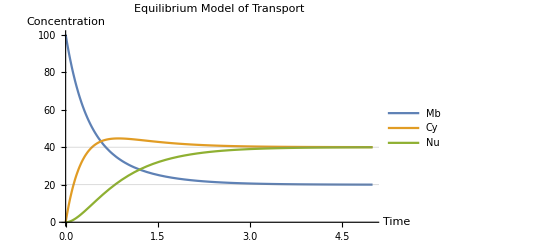

```mathematica
Plot[Evaluate[{Mb[t],Cy[t],Nu[t]}/.sol],{t,0,5},PlotRange-> Full, GridLines->{{20,0,40,0}},PlotLegends->{"Mb","Cy","Nu"},AxesLabel->{"Time","Concentration"},PlotLabel->"Equilibrium Model of Transport"] (* Couldn't figure out how to plug in m, c, n to GridLines, or change colors :/ *)
```

### Problem 1C

```mathematica
Manipulate[
parameters ={f1-> f1val,r1 -> r1val, f2 -> f2val,r2 -> r2val};
sol2 = NDSolve[sys/.parameters,{Mb, Cy,Nu},{t,0,200}];
Plot[Evaluate[{Mb[t],Cy[t],Nu[t]}/.sol2],{t,0,40},PlotRange-> Full, PlotLegends->{"Mb","Cy","Nu"},AxesLabel->{"Time","Concentration"},PlotLabel->"Equilibrium Model of Transport"],{{f1val,2},0,20},{{r1val,1},0,20},{{f2val,1},0,20},{{r2val,1},0,20}]
```

### Problem 2

```mathematica
sys2= {x'[t] ==  Xmax*kd^n1/(z[t]^n1+kd^n1)  -dx*x[t], (* Input function describes z repression of x *)
z'[t] ==  Zmax*x[t]-dz*z[t],
x[0] == 0.1, z[0] == 0};
Manipulate[
param2 = {Xmax -> XmaxVal,Zmax -> ZmaxVal,kd -> kdVal, n1-> 20, dx->1, dz->1};
Soln2 = NDSolve[sys2/.param2,{x,z},{t,0,100}];
Plot[{x[t]/.Soln2,z[t]/.Soln2},{t,0,20},PlotRange->{0,10},PlotStyle->{{Blue,Thick},{Magenta,Thick}}, PlotLegends-> {"x","z"}, AxesLabel->{"Time","Concentration"},PlotLabel->"Simple Negative Feedback: No Feedback"],{XmaxVal,10,10,0.1,Appearance->"Labeled"},
{ZmaxVal,0.7,10,0.1,Appearance->"Labeled"},
{kdVal,10,20,1,Appearance->"Labeled"}
]
```

```mathematica
sys2B= {x'[t] ==  Xmax*kd^n1/(z[t]^n1+kd^n1)  -dx*x[t], (* Input function describes z repression of x *)
z'[t] ==  Zmax*x[t]-dz*z[t],
x[0] == 0.1, z[0] == 0};
Manipulate[
param2B = {Xmax -> XmaxVal,Zmax -> ZmaxVal,kd -> kdVal, n1-> 20, dx->1, dz->1};
Soln2B = NDSolve[sys2B/.param2B,{x,z},{t,0,100}];
Plot[{x[t]/.Soln2B,z[t]/.Soln2B},{t,0,20},PlotRange->{0,10},PlotStyle->{{Blue,Thick},{Magenta,Thick}}, PlotLegends-> {"x","z"},AxesLabel->{"Time","Concentration"},PlotLabel->"Simple Negative Feedback: Strong Feedback"],{XmaxVal,10,10,0.1,Appearance->"Labeled"},
{ZmaxVal,1.5,10,0.1,Appearance->"Labeled"},
{kdVal,1,20,1,Appearance->"Labeled"}
]
```

### Problem 3

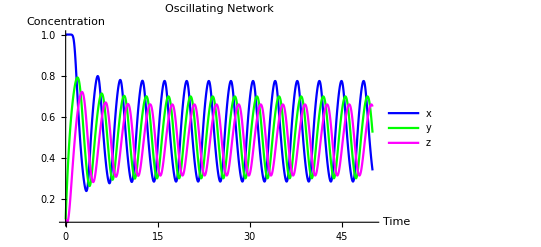

```mathematica
sys3= {x'[t] == Xmax*kz^nx/(z[t]^nx+kz^nx)-dx*x[t], 
y'[t] ==  Ymax* x[t]^ny/(x[t]^ny+kx^ny)- dy*y[t], 
z'[t] ==  Zmax* y[t]^nz/(y[t]^nz+ky^nz)- dz*z[t],
x[0] == 1, y[0] == 0.1, z[0] == 0.1};
param3 = {Xmax -> 1,Ymax-> 1,Zmax-> 1, dx -> 1,dy -> 1,dz -> 1,kx -> 0.5, ky -> 0.5,kz -> 0.5, nx -> 8,  ny ->4, nz -> 4};
Soln3 = NDSolve[sys3/.param3,{x,y,z},{t,0,100}];
Plot[{x[t]/.Soln3,y[t]/.Soln3,z[t]/.Soln3},{t,0,50},PlotRange->Full,PlotStyle->{{Blue,Thick},{Green,Thick},{Magenta,Thick}}, PlotLegends-> {"x","y","z"},AxesLabel->{"Time","Concentration"},PlotLabel->"Oscillating Network"]
```